```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
directories = DirectoryName/@FileNames["log.txt","",∞]
```

{build/particle_method_test/,build/phase_space_sheets_method_test.5/}

```mathematica
directories="build/phase_space_sheets_method_test.5";
```

```mathematica
ρ1Dfiles=FileNames["1D_DIFFr_a.strip.dat.gz",directories,∞];
```

```mathematica
ρ1D=Import[#]&/@ρ1Dfiles;
```

```mathematica
Length[ρ1D⟦1,;;,1⟧]
```

932

```mathematica
Manipulate[GraphicsGrid[{
ListPlot/@ρ1D⟦;;,i,;;⟧
},ImageSize->500],{i,1,900,10}]
```

```mathematica
Dx1Dfiles=FileNames["1D_sheets_Dx.strip.dat.gz",directories,∞];
```

```mathematica
Dx1D=Import[#]&/@Dx1Dfiles;
```

```mathematica
vx1Dfiles=FileNames["1D_sheets_vx.strip.dat.gz",directories,∞];
```

```mathematica
vx1D=Import[#]&/@vx1Dfiles;
```

```mathematica
ϕ1Dfiles=FileNames["1D_DIFFphi_a.strip.dat.gz",directories,∞];
```

```mathematica
ϕ1D=Import[#]&/@ϕ1Dfiles;
```

```mathematica
K1Dfiles=FileNames["1D_DIFFK_a.strip.dat.gz",directories,∞];
K1D=Import[#]&/@K1Dfiles;
```

```mathematica
α1Dfiles=FileNames["1D_DIFFalpha_a.strip.dat.gz",directories,∞];
```

```mathematica
α1D=Import[#]&/@α1Dfiles;
```

```mathematica
px1Dfiles=FileNames["particle_x.dat.gz",directories,∞];
px1D=Import[#]&/@px1Dfiles;
vx1Dfiles=FileNames["particle_vx.dat.gz",directories,∞];
```

```mathematica
vx1D=Import[#]&/@vx1Dfiles;
```

```mathematica
α1D⟦1,1,;;⟧
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vx1D⟦1,2,1⟧
```

1.53223×10^-6

```mathematica
Table[px1D⟦1,1,i⟧,{i,1,32}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{}⟦1,1,1⟧,{}⟦1,1,2⟧,{}⟦1,1,3⟧,{}⟦1,1,4⟧,{}⟦1,1,5⟧,{}⟦1,1,6⟧,{}⟦1,1,7⟧,{}⟦1,1,8⟧,{}⟦1,1,9⟧,{}⟦1,1,10⟧,{}⟦1,1,11⟧,{}⟦1,1,12⟧,{}⟦1,1,13⟧,{}⟦1,1,14⟧,{}⟦1,1,15⟧,{}⟦1,1,16⟧,{}⟦1,1,17⟧,{}⟦1,1,18⟧,{}⟦1,1,19⟧,{}⟦1,1,20⟧,{}⟦1,1,21⟧,{}⟦1,1,22⟧,{}⟦1,1,23⟧,{}⟦1,1,24⟧,{}⟦1,1,25⟧,{}⟦1,1,26⟧,{}⟦1,1,27⟧,{}⟦1,1,28⟧,{}⟦1,1,29⟧,{}⟦1,1,30⟧,{}⟦1,1,31⟧,{}⟦1,1,32⟧}

```mathematica
Manipulate[ListPlot[Table[ϕ1D⟦1,j,i⟧,{i,1,Length[α1D⟦1,1,;;⟧]}]],{j,800,1000,1}]
```

```mathematica
Manipulate[GraphicsGrid[{
ListPlot/@ϕ1D⟦;;,i,;;⟧
},ImageSize->500],{i,1,4,1}]
```

```mathematica
Manipulate[ListPlot[Table[{Dx1D⟦1,j,i⟧+(i-1)/64,vx1D⟦1,j,i⟧},{i,1,Length[Dx1D⟦1,1,;;⟧]}]],{j,100,900,10}]
```

```mathematica
Length[px1D⟦1,1,;;⟧]
```

32768

```mathematica
Manipulate[ListPlot[Table[{px1D⟦1,j,i⟧,vx1D⟦1,j,i⟧},{i,1,Length[px1D⟦1,1,;;⟧]}]],{j,800,1000,1}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 1000 of {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«14»},«49»,«882»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
vx1D⟦1,1,1⟧
```

0

```mathematica
Manipulate[ListPlot[Table[vx1D⟦1,j,i⟧,{i,1,Length[Dx1D⟦1,1,;;⟧]}]],{j,1,13,1}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

```mathematica
Length[Dx1D⟦1,;;,1⟧]
```

19

```mathematica
Dx1D⟦1,1,;;⟧
```

{0,-0.0001525,-0.0002847,-0.0003963,-0.0004867,-0.0005557,-0.0006029,-0.0006279,-0.0006306,-0.0006108,-0.0005682,-0.0005029,-0.0004147,-0.0003038,-0.0001702,-0.000014,0.0001645,0.000365,0.0005873,0.0008309,0.0010953,0.0013799,0.0016842,0.0020075,0.002349,0.0027078,0.0030832,0.0034741,0.0038796,0.0042986,0.00473,0.0051726,0.0056252,0.0060865,0.0065553,0.0070303,0.00751,0.0079931,0.0084783,0.008964,0.0094491,0.009932,0.0104113,0.0108858,0.011354,0.0118146,0.0122664,0.012708,0.0131384,0.0135562,0.0139605,0.0143501,0.0147241,0.0150815,0.0154214,0.015743,0.0160456,0.0163286,0.0165911,0.0168329,0.0170533,0.0172519,0.0174285,0.0175827,0.0177144,0.0178233,0.0179095,0.0179728,0.0180134,0.0180312,0.0180266,0.0179996,0.0179505,0.0178797,0.0177874,0.017674,0.01754,0.0173858,0.017212,0.017019,0.0168074,0.0165779,0.0163311,0.0160676,0.015788,0.0154932,0.0151838,0.0148605,0.0145242,0.0141755,0.0138153,0.0134445,0.0130637,0.0126738,0.0122757,0.0118703,0.0114583,0.0110406,0.0106181,0.0101917,0.0097623,0.0093307,0.0088978,0.0084645,0.0080317,0.0076002,0.007171,0.006745,0.0063229,0.0059057,0.0054942,0.0050894,0.0046919,0.0043028,0.0039229,0.0035529,0.0031937,0.0028461,0.0025108,0.0021888,0.0018806,0.001587,0.0013089,0.0010468,0.0008014,0.0005735,0.0003635,0.0001722}

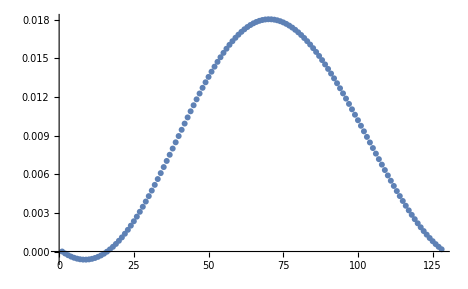

```mathematica
ListPlot[Table[Dx1D⟦1,1,i⟧,{i,1,Length[Dx1D⟦1,1,;;⟧]}]]
```

```mathematica
ListPlot[Table[Dx1D[1,1,i],{i,1,Length[Dx1D[1,1,;;]]}]]
```

-Graphics-

```mathematica
Manipulate[GraphicsGrid[{
ListPlot/@(Dx1D⟦;;,i,;;⟧+1)
},ImageSize->500],{i,1,100,1}]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

```mathematica
ρ1D⟦;;,50,;;⟧
```

{{0.0331069,0.0323809,0.0316631,0.031062,0.0306682,0.0305407,0.0306986,0.0311181,0.0317364,0.0324606,0.0331807,0.0337866,0.0341853,0.0343148,0.0341547,0.0337301}}

```mathematica
ρ1D⟦;;,1,;;⟧
```

{{0.121586,0.119229,0.116888,0.114918,0.113623,0.113203,0.113723,0.115103,0.117128,0.119489,0.121825,0.123782,0.125065,0.125481,0.124966,0.123599}}